```mathematica
E^x*Sin[x]
```

ⅇ^x Sin[x]

```mathematica
Log[E^x+E^-x]
```

Log[ⅇ^-x+ⅇ^x]

```mathematica
F[x_]:=Log[E^x+E^-x]
```

```mathematica
F[0]
```

Log[2]

```mathematica
N[%]
```

0.693147

```mathematica
F[x_]:=E^x*Sin[x]
```

```mathematica
F[0]
```

F[0]

```mathematica
F[x_]:=E^x*Sin[x]
```

```mathematica
F[0]
```

0

```mathematica
F[20]
```

ⅇ^20 Sin[20]

```mathematica
N[%]
```

4.42929×10^8

```mathematica
Sin[45 Degree]
```

1/(√2)

```mathematica
N[Sin[60 Degree]]
```

0.866025

```mathematica
F[x_,y_]:=Sin[x^2+y^2]
```

```mathematica
F[0,10]
```

Sin[100]

```mathematica
F[x_,y_]:=ArcTan[y/x]
```

```mathematica
F[1,2]
```

ArcTan[2]

```mathematica
N[%]
```

1.10715

```mathematica
∑_(N=1)^100 N
```

5050

```mathematica
Sum[n,{n,1,100}]
```

5050

```mathematica
Sum[i,{i,1,n}]
```

1/2 n (1+n)

```mathematica
Sum[i,{i,2,99}]
```

4949

```mathematica
fos[x_]:=Sum[i^x,{i,1,n}]
```

```mathematica
fos[2]
```

1/6 n (1+n) (1+2 n)

```mathematica
fos[4]
```

1/30 n (1+n) (1+2 n) (-1+3 n+3 n^2)

```mathematica
∑_(i=1)^n i
```

1/2 n (1+n)

```mathematica
Sum[1/2^x,{x,0,∞}]
```

2

```mathematica
(*if there is no 1 at the front*)
Sum[1/2^x,{x,1,∞}]
```

1

```mathematica
Sum[j,{i,1,7},{j,1,i}]
```

84

```mathematica
∑_(i=1)^7 ∑_(j=1)^i j
```

84

```mathematica
Product[i^2,{i,1,6}]
```

518400

```mathematica
Product[2j,{i,1,4},{j,1,i}]
```

294912

```mathematica
Product[i,{i,1,n}]
```

n!

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→1/(2 a)(-b-√(b^2-4 a c))},{x→1/(2 a)(-b+√(b^2-4 a c))}}

```mathematica
NSolve[x^2+9x+2==0,x]
```

{{x→-8.772},{x→-0.227998}}

```mathematica
NSolve[a x^3+b x^2+c x+d==0,x]
```

{{x→-(0.333333 b)/a-(0.419974 (-1. b^2+3. a c))/(a (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3))+1/a 0.264567 (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3)},{x→-(0.333333 b)/a+((0.209987+0.363708 ⅈ) (-1. b^2+3. a c))/(a (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3))-1/a(0.132283-0.229122 ⅈ) (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3)},{x→-(0.333333 b)/a+((0.209987-0.363708 ⅈ) (-1. b^2+3. a c))/(a (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3))-1/a(0.132283+0.229122 ⅈ) (-2. b^3+9. a b c-27. a^2 d+√(4. (-1. b^2+3. a c)^3+(-2. b^3+9. a b c-27. a^2 d)^2))^(1/3)}}

```mathematica
NSolve[x^5+16 x^4+7 x^3+17 x^2+11x+5==0]
```

{{x→-15.6187},{x→-0.386706-0.39778 ⅈ},{x→-0.386706+0.39778 ⅈ},{x→0.196058-1.00086 ⅈ},{x→0.196058+1.00086 ⅈ}}

```mathematica
NSolve[Sin[ArcCos[x^2-x]]==1]
```

{{x→1.},{x→1.},{x→0.},{x→0.}}

```mathematica
Solve[a x^2+b x+c==0,c]
```

{{c→-b x-a x^2}}

```mathematica
Solve[ {x^2+5 y+6==0,x+y==1},{x,y}]
```

{{y→1/2 (-3-ⅈ √19),x→1/2 (5+ⅈ √19)},{y→1/2 (-3+ⅈ √19),x→1/2 (5-ⅈ √19)}}

```mathematica
NSolve[ {5 x^2+6 y^2-9==0,x+y==1},{x,y}]
```

{{x→1.3006,y→-0.300602},{x→-0.209693,y→1.20969}}

```mathematica
NSolve[ {x+y+z-9==0,x+4y==4,2x+3y+z==9},{x,y,z}]
```

{{x→-4.,y→2.,z→11.}}

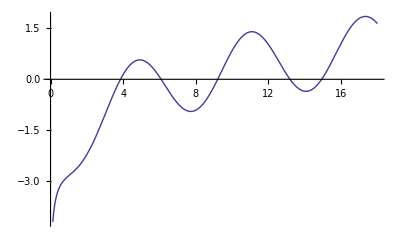

```mathematica
Plot[Log[x]-Sin[x]-2,{x,0,18}]
```

```mathematica
FindRoot[Log[x]-Sin[x]==2,{x,4}]
```

{x→3.85128}

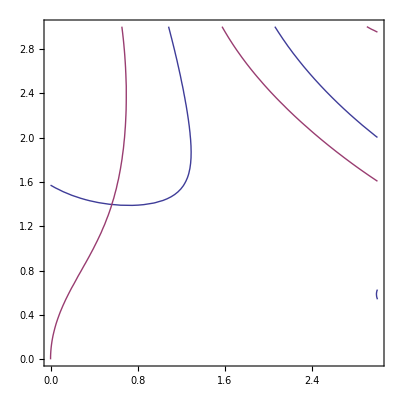

```mathematica
ContourPlot[{Sin[x y]==Sin[x]+Cos[y],Cos[x y]==Sin[x]+Cos[y]},{x,0,3},{y,0,3}]
```

```mathematica
FindRoot[{Sin[x y]==Sin[x]+Cos[y],Cos[x y]==Sin[x]+Cos[y]},{x,0.6},{y,1.4}]
```

{x→0.562547,y→1.39615}

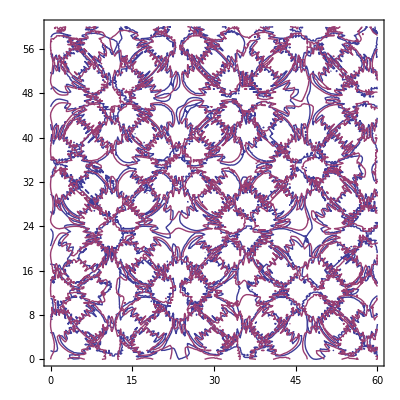

```mathematica
ContourPlot[{Sin[x y]==Sin[x]+Cos[y],Cos[x y]==Sin[x]+Cos[y]},{x,0,60},{y,0,60}]
```